## Previous functions

### Gram Matrix Generation

```mathematica
Coeff[n_,m_,Nt_,J_]:=Module[
{d,factor1,zmin,zmax,factor2},
d=Abs[m-n];
factor1 = ((Nt-d)!*d!*(Nt-J)!)/(Nt!*Nt!);
zmin=Max[{d-J,0}];
zmax=Min[{Nt-J,d}];
factor2=Total[Table[(-1)^z*((Nt-z)!*(J+z)!)/((Nt-J-z)!*(d-z)!*(J-d+z)!*z!),{z,zmin,zmax}]];
factor1*factor2
]

GMatrix[Nt_,J_]:=Table[Coeff[a-1,b-1,Nt,J],{a,Nt},{b,Nt}];
SMatrix[Nt_,J_]:=MatrixPower[N[GMatrix[Nt,J]],1/2];
```

### Square Root Measurement

```mathematica
ProbabilitySRM[Ntotal_,J_]:=Ntotal*(SMatrix[Ntotal,J][[1,1]])^2;
```

### Real Semi Definite Programming

```mathematica
ProbabilitySDPR[Ntotal_,J_]:=Module[
{Es,GSqrt,ObjFunction,Constraints,Solution},

GSqrt=SMatrix[Ntotal,J];
Es=Table[Table[Subscript[x,k,i,j],{i,Ntotal},{j,Ntotal}],{k,Ntotal}];
ObjFunction=-Total[Table[GSqrt[[k]].Es[[k]].GSqrt[[k]],{k,Ntotal}]];
Constraints=Join[{Total[Es]==IdentityMatrix[Ntotal]},
Table[VectorGreaterEqual[{Es[[k]],ConstantArray[0,{Ntotal,Ntotal}]}],{k,Ntotal}]];

Solution=SemidefiniteOptimization[ObjFunction,Constraints,Flatten[Es]];
-ObjFunction/.Solution
]
```

### Complex Semi Definite Programming

```mathematica
ProbabilitySDPC[Ntotal_,J_]:=Module[
{ReEs,ImEs,Es,BlockEs,Vars,GSqrt,
ObjFunction,Constraint1,Constraint2,Constraints,Solution},

GSqrt=SMatrix[Ntotal,J];
ReEs=Table[Table[Subscript[x,k,i,j],{i,Ntotal},{j,Ntotal}],{k,Ntotal}];
ImEs=Table[Table[Subscript[y,k,i,j],{i,Ntotal},{j,Ntotal}],{k,Ntotal}];
Es=Table[ReEs[[k]]+I*ImEs[[k]],{k,Ntotal}];
BlockEs=Table[
ArrayFlatten[{{ReEs[[k]],-ImEs[[k]]},{ImEs[[k]],ReEs[[k]]}}],
{k,Ntotal}
];
Vars=Join[Flatten[ReEs],Flatten[ImEs]];

ObjFunction=-Sum[Re[GSqrt[[k]].Es[[k]].GSqrt[[k]]],{k,Ntotal}];

Constraint1=Total[Es]==IdentityMatrix[Ntotal];
Constraint2=Table[
VectorGreaterEqual[{BlockEs[[k]],ConstantArray[0,{2*Ntotal,2*Ntotal}]}],
{k,Ntotal}
];
Constraints=Join[{Constraint1},Constraint2];

Solution=SemidefiniteOptimization[ObjFunction,Constraints,Vars];
-ObjFunction/.Solution
]
```

## Examples

```mathematica
Nt=10;
valuesx=Range[0,Nt];
valuesSRM=Table[ProbabilitySRM[Nt,J],{J,0,Nt}]
valuesSDPR=Table[ProbabilitySDPR[Nt,J],{J,0,Nt}]
valuesSDPC=Table[ProbabilitySDPC[Nt,J],{J,0,Nt}]
```

{9.94854,9.96756,9.99186,9.99635,9.94517,9.79007,9.4643,8.86639,7.81516,5.89921,1.}

{9.94854,9.96756,9.99186,9.99635,9.94517,9.79007,9.4643,8.86639,7.81516,5.89921,1.}

{9.94854,9.96756,9.99186,9.99635,9.94517,9.79007,9.4643,8.86639,7.81516,5.89921,1.}

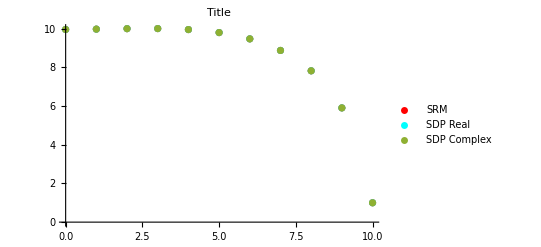

```mathematica
ListPlot[
{Transpose[{valuesx,valuesSRM}],
Transpose[{valuesx,valuesSDPR}],
Transpose[{valuesx,valuesSDPC}]},
PlotStyle->{Red,Cyan,SpringGreen},
PlotLegends->{"SRM","SDP Real","SDP Complex"},
FrameLabel->{"J","Psuccess"},
PlotLabel->"Title"
]
```